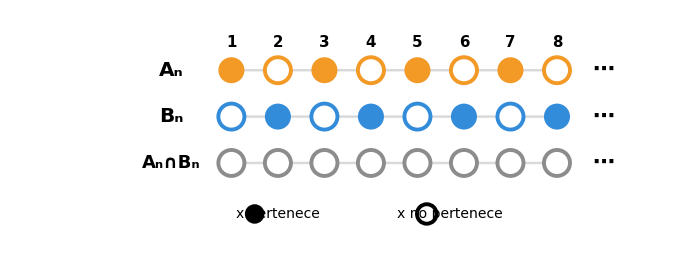
Ω = {x}
-Graphics-

```mathematica
nCols=8;

colorA=RGBColor[0.95,0.6,0.15];
colorB=RGBColor[0.2,0.55,0.85];
colorInter=RGBColor[0.55,0.55,0.55];

yA=2;yB=1;yInter=0;
rDot=0.28;

inA[n_]:=OddQ[n];
inB[n_]:=EvenQ[n];

cellMarker[center_,color_,filled_]:=If[filled,{color,Disk[center,rDot]},{White,Disk[center,rDot],color,Thickness[0.004],Circle[center,rDot]}];

lineaGuia[y_]:={LightGray,Thickness[0.0025],Line[{{1,y},{nCols,y}}]};

filaA=Table[cellMarker[{k,yA},colorA,inA[k]],{k,1,nCols}];
filaB=Table[cellMarker[{k,yB},colorB,inB[k]],{k,1,nCols}];
filaInter=Table[cellMarker[{k,yInter},colorInter,False],{k,1,nCols}];

etiquetasColumnas=Table[Text[Style[k,15,Bold],{k,yA+0.6}],{k,1,nCols}];

etiquetasFilas={Text[Style["Aₙ",20,Bold],{-0.3,yA},{1,0}],Text[Style["Bₙ",20,Bold],{-0.3,yB},{1,0}],Text[Style["Aₙ∩Bₙ",18,Bold],{-0.3,yInter},{1,0}]};

elipsisCol=nCols+1;
elipsis={Text[Style["⋯",22,Bold],{elipsisCol,yA}],Text[Style["⋯",22,Bold],{elipsisCol,yB}],Text[Style["⋯",22,Bold],{elipsisCol,yInter}]};

yLeyenda=yInter-1.1;
leyendaManual={Black,Disk[{1.5,yLeyenda},0.21],Text[Style["x pertenece",14],{2.0,yLeyenda},{-1,0}],White,Disk[{5.2,yLeyenda},0.21],Black,Thickness[0.004],Circle[{5.2,yLeyenda},0.21],Text[Style["x no pertenece",14],{5.7,yLeyenda},{-1,0}]};

grafico=Graphics[{lineaGuia[yA],lineaGuia[yB],lineaGuia[yInter],filaA,filaB,filaInter,etiquetasColumnas,etiquetasFilas,elipsis,leyendaManual},PlotRange->{{-2.6,elipsisCol+0.7},{yLeyenda-0.5,yA+1.0}},ImageSize->700];

imagenFinal=Column[{Style["Ω = {x}",17,Bold],grafico},Alignment->Center,Spacings->0.7];

imagenFinal
```

```mathematica
Export["extra1_P1.png",imagenFinal,Background->White,ImageResolution->300];
```

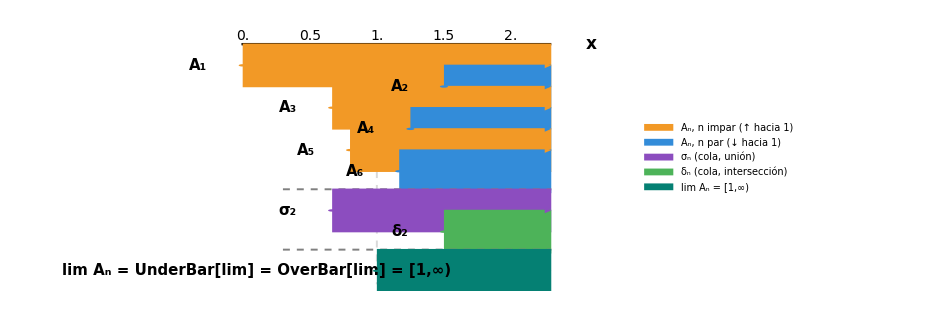

```mathematica
nMin=1;nMax=6;
sep=0.55;
xMaxPlot=2.3;

xn[n_]:=1+(-1)^n/n;

colorImpar=RGBColor[0.95,0.6,0.15];  (*crecen hacia 1 por abajo*)
colorPar=RGBColor[0.2,0.55,0.85];    (*decrecen hacia 1 por arriba*)
colorSigma=RGBColor[0.55,0.3,0.75];
colorDelta=RGBColor[0.3,0.7,0.35];
colorLim=RGBColor[0.02,0.5,0.45];

subInd[n_Integer]:=StringJoin[Characters[ToString[n]]/. {"0"->"₀","1"->"₁","2"->"₂","3"->"₃","4"->"₄","5"->"₅","6"->"₆","7"->"₇","8"->"₈","9"->"₉"}];

rDot=0.03;
closedDot[center_,col_]:={col,Disk[center,rDot]};

rayo[xStart_,y_,col_]:={col,Thickness[0.045],CapForm["Round"],Arrowheads[0.03],Arrow[{{xStart,y},{xMaxPlot,y}}],closedDot[{xStart,y},col]};

(*----------filas A_n,n=1,...,6----------*)
filasA=Table[Module[{y,x,col},y=-(n-nMin) sep;
x=xn[n];
col=If[OddQ[n],colorImpar,colorPar];
{rayo[x,y,col],Text[Style["A"<>subInd[n],15,Bold],{x-0.33,y}]}],{n,nMin,nMax}];

yUltimaA=-(nMax-nMin) sep;

(*----------ejemplo de colas:sigma_2 y delta_2 (apartado 1)----------*)
sigma2=2/3;delta2=3/2;

ySep1=yUltimaA-0.85 sep;
ySigma=ySep1-sep;
yDelta=ySigma-sep;

filaSigma={rayo[sigma2,ySigma,colorSigma],Text[Style["σ₂",15,Bold],{sigma2-0.33,ySigma}]};
filaDelta={rayo[delta2,yDelta,colorDelta],Text[Style["δ₂",15,Bold],{delta2-0.33,yDelta}]};

lineaSep1={Gray,Dashed,Thickness[0.002],Line[{{0.3,ySep1},{xMaxPlot,ySep1}}]};

(*----------fila final:lim A_n=[1,∞) (liminf=limsup)----------*)
ySep2=yDelta-0.85 sep;
yLim=ySep2-sep;

filaLim={rayo[1,yLim,colorLim],Text[Style[Row[{"lim Aₙ = ",UnderBar[Style["lim",14,Bold]]," = ",OverBar[Style["lim",14,Bold]]," = [1,∞)"}],15,Bold],{1-0.9,yLim}]};

lineaSep2={Gray,Dashed,Thickness[0.002],Line[{{0.3,ySep2},{xMaxPlot,ySep2}}]};

(*----------eje real y línea guía en x=1----------*)
ejeReal={Black,Thickness[0.0025],Line[{{0,0.55},{xMaxPlot,0.55}}],Table[Line[{{k,0.52},{k,0.58}}],{k,0,2,0.5}],Table[Text[Style[k,14],{k,0.75}],{k,0,2,0.5}],Text[Style["x",17,Bold],{xMaxPlot+0.3,0.55}]};

guiaUno={LightGray,Dashed,Thickness[0.002],Line[{{1,0.5},{1,yLim-0.35}}]};

grafico=Graphics[{ejeReal,guiaUno,filasA,lineaSep1,filaSigma,filaDelta,lineaSep2,filaLim},PlotRange->{{-1.2,xMaxPlot+0.5},{yLim-0.4,0.95}},AspectRatio->0.45,ImageSize->700];

leyenda=SwatchLegend[{colorImpar,colorPar,colorSigma,colorDelta,colorLim},{"Aₙ, n impar (↑ hacia 1)","Aₙ, n par (↓ hacia 1)","σₙ (cola, unión)","δₙ (cola, intersección)","lim Aₙ = [1,∞)"},LabelStyle->Directive[FontSize->14],LegendMarkerSize->18];

imagenFinal=Legended[grafico,leyenda];

imagenFinal
```

```mathematica
Export["extra1_P2.png",imagenFinal,Background->White,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["extra1_P2.png"]]]
```